```mathematica
p = 1/3;
sum = Sum[Binomial[n,k]*((p^k)*(1-p)^(n-k))^q,{k,0,n}];

limit = 1/(1-q)*Limit[Log[sum]/Log[3^n], {n->Infinity}];
```

ConditionalExpression[(-q Log[3/2]+Log[1+2^-q])/((1-q) Log[3]), q Log[3/2]>Log[1+2^-q]]

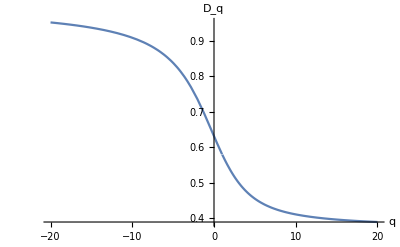

```mathematica
limitWithoutCondition[q0_] =(-q Log[3/2]+Log[1+2^-q])/((1-q) Log[3])/. q-> q0;
Plot[limitWithoutCondition[q], {q, -20, 20}, AxesLabel -> {q,Subscript[D, q]}]
```

```mathematica
Limit[limitWithoutCondition[q], q->1]
limitWithoutCondition[q] /. q-> 2
FullSimplify[Limit[limitWithoutCondition[q], q->-Infinity]]
Limit[limitWithoutCondition[q], q->Infinity]
```

Log[27/4]/Log[27]

-(Log[5/4]-2 Log[3/2])/Log[3]

1

Log[3/2]/Log[3]

0.36907